```mathematica
f={t-Sin[t],1-Cos[t]};
f1=Simplify[D[f,t]]
f2=Simplify[D[f1,t]]
```

{1-Cos[t],Sin[t]}

{Sin[t],Cos[t]}

```mathematica
cross =Simplify[Cross[{f1[[1]],f1[[2]],0},{f2[[1]],f2[[2]],0}]]
```

{0,0,-1+Cos[t]}

```mathematica
curvature=Simplify[cross/((f1[[1]]^2+f1[[2]]^2)^(3/2))]
```

{0,0,-1/(2 √(2-2 Cos[t]))}

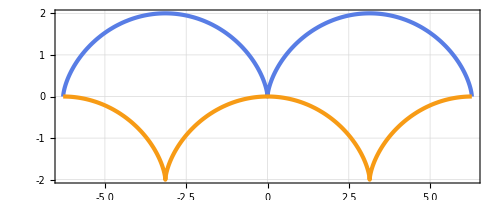

```mathematica
Show[
ParametricPlot[{{t-Sin[t],1-Cos[t]},{t+Sin[t],-1+Cos[t]}},{t,-2π,2π},PlotTheme->"Business"]
]
```

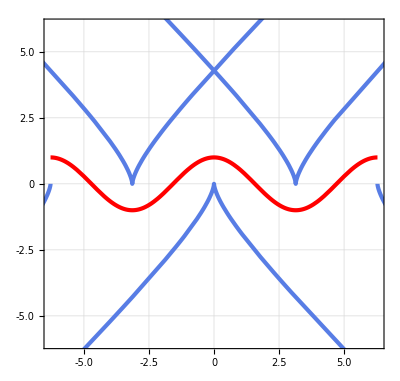

```mathematica
Show[
ParametricPlot[{t-(-Sin[t]+(-Sin[t])^3)/(-Cos[t]),Cos[t]+(1+Sin[t]^2)/(-Cos[t])},{t,-2π,2π},PlotTheme->"Business"],
Plot[Cos[x],{x,-2π,2π},PlotTheme->"Business",PlotStyle->Red],
PlotRange->{{-2π,2π},{-6,6}}
]
```

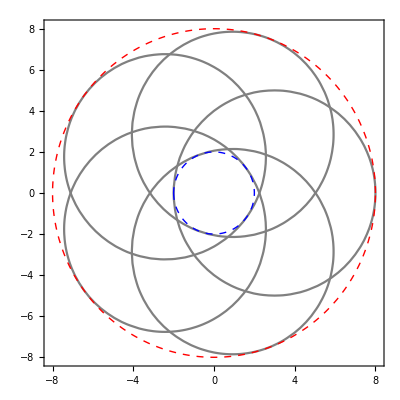

```mathematica
R=5;r=3;
Show[
ContourPlot[(x-r Cos[(2π)/5])^2+(y-r Sin[(2π)/5])^2==R^2,{x,-r-R,r+R},{y,-r-R,r+R},ContourStyle->Gray],
ContourPlot[(x-r Cos[(4π)/5])^2+(y-r Sin[(4π)/5])^2==R^2,{x,-r-R,r+R},{y,-r-R,r+R},ContourStyle->Gray],
ContourPlot[(x-r Cos[(6π)/5])^2+(y-r Sin[(6π)/5])^2==R^2,{x,-r-R,r+R},{y,-r-R,r+R},ContourStyle->Gray],
ContourPlot[(x-r Cos[(8π)/5])^2+(y-r Sin[(8π)/5])^2==R^2,{x,-r-R,r+R},{y,-r-R,r+R},ContourStyle->Gray],
ContourPlot[(x-r Cos[(10π)/5])^2+(y-r Sin[(10π)/5])^2==R^2,{x,-r-R,r+R},{y,-r-R,r+R},ContourStyle->Gray],
ParametricPlot[{{(R+r)Cos[t],(R+r)Sin[t]},{(r-R)Cos[t],(r-R)Sin[t]}},{t,0,2π},PlotStyle->{{Red,Thick,Dashed},{Blue,Thick,Dashed}}],
PlotRange->{{-r-R-0.1,r+R+0.1},{-r-R-0.1,r+R+0.1}}
]
```

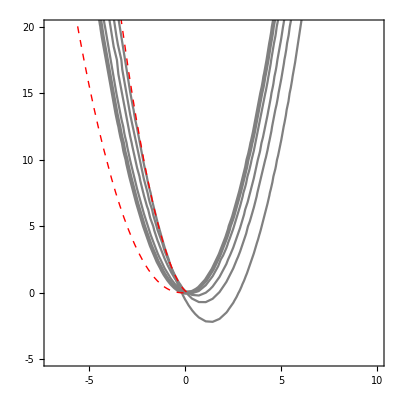

```mathematica
a1=0.1;a2=0.3;a3=0.6;a4=0.9;a5=1.3;
Show[
ContourPlot[(x-a1)^2-y==a1^3,{x,-20,20},{y,-40,30},PlotTheme->"Business",ContourStyle->Gray],
ContourPlot[(x-a2)^2-y==a2^3,{x,-20,20},{y,-40,30},ContourStyle->Gray],
ContourPlot[(x-a3)^2-y==a3^3,{x,-20,20},{y,-40,30},ContourStyle->Gray],
ContourPlot[(x-a4)^2-y==a4^3,{x,-20,20},{y,-40,30},ContourStyle->Gray],
ContourPlot[(x-a5)^2-y==a5^3,{x,-20,20},{y,-40,30},ContourStyle->Gray],
ParametricPlot[{1/2 (2 t-3 t^2),1/4 t^3 (-4+9 t)},{t,-100,50},PlotStyle->{Red,Thick,Dashed}],
PlotRange->{{-7,10},{-5,20}}
]
```

```mathematica
U[x_,y_,a_]=(x-a)^2-y-a^3;
Solve[U[x,y,a]==0&&D[U[x,y,a],a]==0,{x,y}]
```

{{x→1/2 (2 a-3 a^2),y→1/4 a^3 (-4+9 a)}}